```mathematica
q[v_]:=0.5*Erfc[v/(√2)];
oneOverN[nd_, p_]:=1/(nd p) (1-(1-p)^nd);
oneOverN2[nd_, p_]:=NIntegrate[(1-p+p x)^(nd-1) (-Log[x]), {x, 0, 1.}];
gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w((k+b)-(1-beta/ns)w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=(k+b)-(1-beta/ns)w x;
g1Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, bkTmp, kFactor, part1, part2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor = ndR oneOverN[nd, pUpdated];
bkTmp = k kFactor + b;
part1 = (-2. ⅇ^(-bla^2/2)  (bkTmp ns+bla (beta-ns) w)+(beta (-1+ns)+ns)√(2 π)w Erfc[bla/(√2)])/(2 ns w √(2 π));

part2 = NIntegrate[gTmp1[x, b, ndR k,beta, ns, w ] Exp[-x^2/2]/Sqrt[2.π ](1-q[x])^(nd-1), {x, -Infinity, bla}];
part1+part2
];
g1NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, bkTmp, kFactor},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor = ndR oneOverN[nd, pUpdated];
bkTmp = k kFactor + b;
(-2. ⅇ^(-bla^2/2)  (bkTmp ns+bla (beta-ns) w)+(beta (-1+ns)+ns)√(2 π)w Erfc[bla/(√2)])/(2 ns w √(2 π))
];
g21Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, kFactor2, bkTmp1, bkTmp2, part1, part2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
kFactor2 = ndR^2 oneOverN2[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
bkTmp2 = k^2 kFactor2 + 2b k kFactor1 + b^2;
part1=1./(2 ns^2)(ⅇ^(-bla^2/2) (beta-ns) √(2/π) w (2 bkTmp1 ns+bla (beta-ns) w)+(bkTmp2 ns^2+(beta-ns)^2 w^2) Erfc[bla/(√2)]);
part2 =NIntegrate[gTmp2[x, b, ndR k,beta, ns, w ] Exp[-x^2/2]/Sqrt[2.π ](1-q[x])^(nd-1), {x, -Infinity, bla}];
part1+part2
];
g21NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, kFactor2, bkTmp1, bkTmp2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
kFactor2 = ndR^2 oneOverN2[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
bkTmp2 = k^2 kFactor2 + 2b k kFactor1 + b^2;
1./(2 ns^2)(ⅇ^(-bla^2/2) (beta-ns) √(2/π) w (2 bkTmp1 ns+bla (beta-ns) w)+(bkTmp2 ns^2+(beta-ns)^2 w^2) Erfc[bla/(√2)])
];
g22Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, bkTmp1, part1, part2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
part1=1/(2 ns^2)(1/w^2 ⅇ^(-bla^2/2) √(2/π) (bkTmp1 ns+bla (beta-ns) w) (bkTmp1 bla ns+beta (2+bla^2) w-(2+2 beta+bla^2) ns w)+(2 beta^2-2 beta (2+beta) ns+(2+beta (2+beta)) ns^2) Erfc[bla/(√2)]);
part2=NIntegrate[(gTmp1[x, b, ndR k, beta, ns, w]^2-gTmp2[x, b, ndR k, beta, ns, w]^2/w^2)Exp[-x^2/2]/Sqrt[2.π ](1-q[x])^(nd-1), {x, -Infinity, bla}];
part1+part2
];
g22NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, kFactor1, bkTmp1},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor1 = ndR oneOverN[nd, pUpdated];
bkTmp1 = k kFactor1 + b;
1/(2 ns^2)(1/w^2 ⅇ^(-bla^2/2) √(2/π) (bkTmp1 ns+bla (beta-ns) w) (bkTmp1 bla ns+beta (2+bla^2) w-(2+2 beta+bla^2) ns w)+(2 beta^2-2 beta (2+beta) ns+(2+beta (2+beta)) ns^2) Erfc[bla/(√2)])
];
betaSolutionNonInt[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21NonInt[b, k, nd, ns, ndR, y, w]-2g1NonInt[b, k, nd, ns, ndR, y, w]+g22NonInt[b, k, nd, ns, ndR, y, w]/ns, {y, 20.}];
betaSolutionInt[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w]+g22Int[b, k, nd, ns, ndR, y, w]/ns, {y, -10., 50.}, Method->"Brent"];
(*****************************************************************************)
```

```mathematica
(*each row of paramsList: b, bk, n, nd, ns*)
paramsList = Import["/home/fangxu/BennaLab/dendrite_familiarity_detection/tmp_data/tmp.csv"];
paramsList//Dimensions
```

{85,5}

```mathematica
bsSize=9;
bSpacing = 0.15;
paramsFunMultipleB[nd_, ns_, bCenter_, bk_, ndR_]:=Module[{betas, bs},
 bs=Table[bCenter + i*bSpacing, {i, -Quotient[bsSize, 2], Quotient[bsSize, 2]}];
betas = Table[betaSolutionInt[b, bk-b, nd, ns, ndR, 1.], {b, bs}]//Quiet; (*note that here we can't always set b=0, kappa = b+kappa *)
Join[{nd, ns, bk, bCenter, ndR,20240305}, betas]
];
(*paramsFunMultipleB[nd_, ns_, bCenter_, bk_, ndR_]:=Module[{betas, bs},
 bs=Table[bCenter + i*bSpacing, {i, -Quotient[bsSize, 2], Quotient[bsSize, 2]}];
betas = Table[betaSolutionNonInt[b, bk-b, nd, ns, ndR, 1.], {b, bs}]//Quiet; (*note that here we can't always set b=0, kappa = b+kappa *)
Join[{nd, ns, bk, bCenter, ndR,20240305}, betas]
];*)
tmpParams = ParallelTable[paramsFunMultipleB[paramsList[[idx, 4]],paramsList[[idx, 5]], paramsList[[idx, 1]], paramsList[[idx, 2]], paramsList[[idx, 3]]], {idx, 1, Length[paramsList]}];
```

```mathematica
Export["/home/fangxu/BennaLab/dendrite_familiarity_detection/tmp_data/params_list_tmp2.csv",tmpParams,"CSV"];
```

```mathematica
(*------------------------------------------------------------------------------------------*)
```

```mathematica
paramsFunNonIntTmp[nd_, ns_, b_, bk_, ndR_]:=Module[{beta}, 
beta = betaSolutionNonInt[b, bk-b, nd, ns, ndR, 1.]//Quiet; (*note that here we can't always set b=0, kappa = b+kappa *)
{nd, ns, bk, b, ndR, beta, 20240305}
];
paramsFunIntTmp[nd_, ns_, b_, bk_, ndR_]:=Module[{beta}, 
beta = betaSolutionInt[b, bk-b, nd, ns, ndR, 1.]//Quiet; (*note that here we can't always set b=0, kappa = b+kappa *)
{nd, ns, bk, b, ndR, beta, 20240305}
];
paramsFunNonIntTmp[300, 200, 2.55, 4.0, 10]
paramsFunIntTmp[300, 200, 2.3, 3.5, 10]
```

{300,200,4.,2.55,10,5.85264,20240305}

{300,200,3.5,2.3,10,3.82157,20240305}

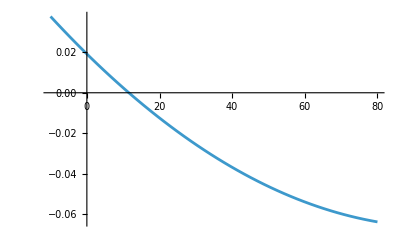

```mathematica
Clear["tmpfun"]
(*tmpfun2[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.]+1/ns g22NonInt[0.,bk,nd,ns,ndR,y,1.];
tmpfun1[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.];*)
tmpfun2[y_, b_, k_, nd_, ns_, ndR_]:=g21Int[b,k,nd,ns,ndR,y,1.]-2 g1Int[b,k,nd,ns,ndR,y,1.]+1/ns g22Int[b,k,nd,ns,ndR,y,1.];
tmpfun1[y_, b_, k_, nd_, ns_, ndR_]:=g21Int[b,k,nd,ns,ndR,y,1.]-2 g1Int[b,k,nd,ns,ndR,y,1.];
nd=1500;ns=40;bk=5.0;b=3.2; ndR=2;
(*Plot[{tmpfun2[y,b,bk-b, nd, ns, ndR], tmpfun1[y, b, bk-b, nd, ns, ndR]}, {y, 0, 80}]*)
Plot[{tmpfun1[y, b, bk-b, nd, ns, ndR]}, {y, -10, 80}]
```

```mathematica
Append
```

Thread::tdlen: Objects of unequal length in {1,2,3}+{1} cannot be combined.

{1}+{1,2,3}

```mathematica
Clear["g1IntTest"];
g1IntTest[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla, bkTmp, kFactor, part1, part2},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
pUpdated =ndR/nd;
kFactor = ndR oneOverN[nd, pUpdated];
bkTmp = k kFactor + b;
part1 = (-2. ⅇ^(-bla^2/2)  (bkTmp ns+bla (beta-ns) w)+(beta (-1+ns)+ns)√(2 π)w Erfc[bla/(√2)])/(2 ns w √(2 π));

part2 = NIntegrate[gTmp1[x, b, ndR k,beta, ns, w ] Exp[-x^2/2]/Sqrt[2.π ](1-q[x])^(nd-1), {x,-Infinity, bla}];
Print[bla];
Print[part1];
Print[part2];
part1+part2
];
g1IntTest[2.55, 1.45, 300, 200, 3, 13.0881, 1.0]
g1NonInt[2.55, 1.45, 300, 200, 3, 4.852638679746199, 1.0]
```

2.32635

0.0934579

0.000386748

0.0938447

0.0140682

```mathematica
NIntegrate[gTmp1[x, 2.55, 3*1.45,4.852638679746199, 200, 1. ] Exp[-x^2/2]/Sqrt[2.π ](1-q[x])^(300-1), {x,2.3, 2.32635}]
```

-0.000189716